```mathematica
PotentialSmearing[Cij α/r]
```

(Cij α Erf[r σ])/r

```mathematica
PotentialSmearing[-3/4 Cij(b*r+c)]
```

-(3 Cij (2 r σ ((b ⅇ^(-r^2 σ^2))/(√π)+c √(σ^2))+(b+2 b r^2 σ^2) Erf[r σ]))/(8 r σ^2)

```mathematica
SphericalLaplacian[Cij α/r Erf[σ*r]]//Simplify
```

-(4 Cij ⅇ^(-r^2 σ^2) α σ^3)/(√π)

{{-1.1711+0.312932 ⅇ^(-3.39296 r^2)+3.35072 (1-ⅇ^(-0.069 r))-0.524/r}}

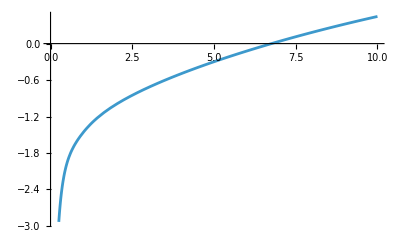

```mathematica
{S,L,J}={1,0,1};
Vij=Potential[{4,4},{S,L,J},"NRScreen"]
Plot[Vij,{r,0,10}]
```

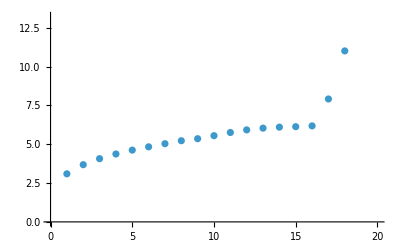

{3.09657,3.68551,4.0725,4.37426,4.62388,4.83615,5.03694,5.2289,5.35902,5.55382,5.75958,5.92542,6.03921,6.10453,6.13384,6.18402,7.91791,11.0138,16.725,27.469}

```mathematica
{Nmax,Rmax,Rmin}={20,10,0.1};
{e,v}=MesonGEM[{4,4},{S,L,J},{Nmax,Rmax,Rmin},"NRScreen"];
ListPlot[e]
e
```

```mathematica
GetRMSRadius[1,L,{Nmax,Rmax,Rmin},v]
```

0.362571

```mathematica
GetRMSRadius[2,L,{Nmax,Rmax,Rmin},v]
```

0.751536

```mathematica
GetRMSRadius[3,L,{Nmax,Rmax,Rmin},v]
```

1.09827

```mathematica
GetRMSRadius[4,L,{Nmax,Rmax,Rmin},v]
```

1.42844

0.424275 ⅇ^(-3.89386 r^2)-0.722206 ⅇ^(-2.39802 r^2)+0.99058 ⅇ^(-1.47682 r^2)-0.758737 ⅇ^(-0.909497 r^2)+0.837468 ⅇ^(-0.560112 r^2)-0.275409 ⅇ^(-0.344944 r^2)+0.607903 ⅇ^(-0.212433 r^2)-0.0339205 ⅇ^(-0.130827 r^2)+0.137004 ⅇ^(-0.0805693 r^2)-0.0694722 ⅇ^(-0.0496184 r^2)+0.03792 ⅇ^(-0.0305574 r^2)-0.0201498 ⅇ^(-0.0188187 r^2)+0.0104261 ⅇ^(-0.0115895 r^2)-0.00523832 ⅇ^(-0.00713736 r^2)+0.00252951 ⅇ^(-0.00439553 r^2)-0.00114858 ⅇ^(-0.00270698 r^2)+0.000471072 ⅇ^(-0.00166709 r^2)-0.000162438 ⅇ^(-0.00102667 r^2)+0.0000411704 ⅇ^(-0.000632275 r^2)-5.59954×10^-6 ⅇ^(-0.000389386 r^2)

1.16217

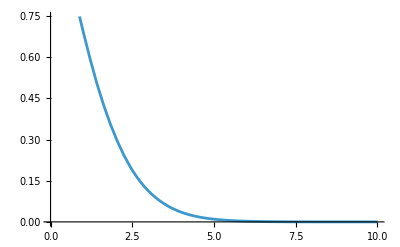

```mathematica
gwv=GetGEMRnlr[1,L,{Nmax,Rmax,Rmin},v]
gwv/.{r->0}
Plot[gwv,{r,0,10}]
```

0.666565

0.817534 ⅇ^(-0.222154 r^2)

0.817534

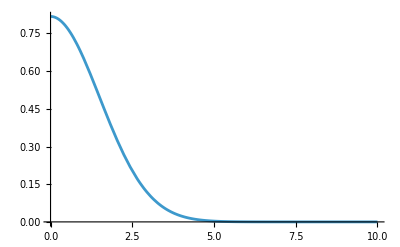

```mathematica
beta=GetSHOBeta[1,L,{Nmax,Rmax,Rmin},v]
swv=GetSHORnlr[1,L,beta]
swv/.{r->0}
Plot[swv,{r,0,10}]
```